# Legacy Elvis Tools

2021 code for solving the generalized Elvis problem in ℝ^2.

This code can be accessed using:

```mathematica
<<ConvexAnalysisGeometry`Legacy`Elvis`
```

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

## Smooth Velocity Set

### Definition

The original Elvis problem solver represents sets as symbols. Upon definition, all properties of the set are computed. This leads to long (potentially unnecessary) upfront cost (as illustrated by the below output of Timing).

Let's begin by parametrically defining a smooth velocity set containing the origin, F0, in terms of the parametric equations for it's boundary.

```mathematica
Clear[F0,t]
Timing@defVel[F0,ℛ[π/4].({Cos[t],4Sin[t]}+{1/2,1/10})]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.109375,Null}

Note we get relatively opaque warnings by internal solvers, and the process of defining this function is computationally expensive, measured in seconds. This is because all relevant representations and related objects for solving the Elvis problem are greedily derived.

### Properties

All properties of Elvis velocity sets are accessed through syntactically interesting methods. We can recover the original boundary parameterization and use it to plot our set.

{(1/2+Cos[t])/(√2)-(1/10+4 Sin[t])/(√2),(1/2+Cos[t])/(√2)+(1/10+4 Sin[t])/(√2)}

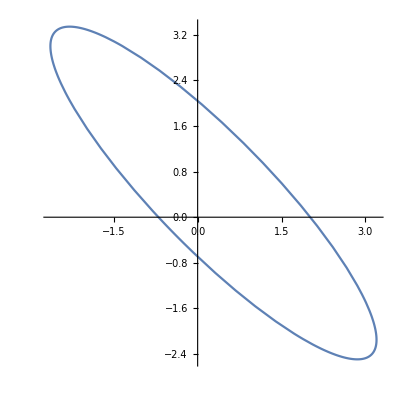

```mathematica
Subscript[F0, bdryParam]
ParametricPlot[%,{t,-π,π}]
```

Now, let's walk through what happened when we called defVel. First, an implicit definition of the boundary was derived and used to compute the support function.

```mathematica
Subscript[F0, bdryCnds]
```

10 x (-79 √2+85 x+150 y)==1199+810 √2 y-850 y^2

```mathematica
Subscript[σ, F0][{x,y}]
```

(2 x+3 y+5 √(17 x^2-30 x y+17 y^2))/(5 √2)

Based on the COT paper, the support is the gauge of the polar (γ_(F^°)=σ_F), so the implicit definition of the boundary of the polar is given by:

```mathematica
(F0^°)_bdryCnds
```

(2 x+3 y+5 √(17 x^2-30 x y+17 y^2))/(5 √2)==1

The associated parametric equation provides us ease in plotting:

```mathematica
(F0^°)_bdryParam
```

{(5 √2 (4 Cos[t]-Sin[t]))/(40+20 Cos[t]+Sin[t]),(5 √2 (4 Cos[t]+Sin[t]))/(40+20 Cos[t]+Sin[t])}

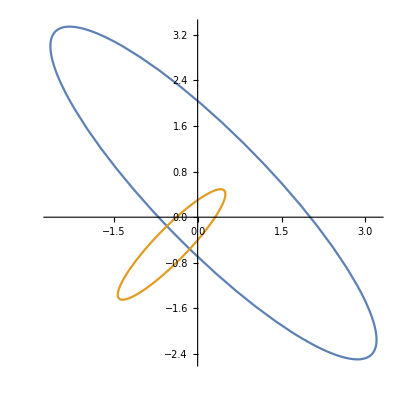

```mathematica
ParametricPlot[{Subscript[F0, bdryParam],(F0^°)_bdryParam},{t,-π,π}]
```

Again, from duality, we can now compute the support of the polar set to get the gauge of F0 (γ_F=σ_(F^°)).

```mathematica
Subscript[γ, F0][{x,y}]
```

(5 √2 (-79 x-81 y+8 √(416 x^2+762 x y+421 y^2)))/1199

For smooth Elvis sets, such as F0, the gradient of the gauge gives the "polar-unit" normal cone ((𝒩̂)_F=∇γ_F). Note in the below figure, the streamlines are always orthogonal to the gauge level sets.

```mathematica
Show[{
ContourPlot[Subscript[γ, F0][{x,y}],{x,-5,5},{y,-5,5},Contours->Range[10],PlotTheme->"Monochrome"],
StreamPlot[Evaluate[∇_{x,y} Subscript[γ, F0][{x,y}]],{x,-5,5},{y,-5,5},StreamScale->None,StreamStyle->Thick]
}]
```

-Graphics-

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

ConvexAnalysisGeometry

ConvexAnalysisGeometry`

ConvexAnalysisGeometry/tutorial/LegacyElvisTools

### Keywords